```mathematica
data=Flatten@Import[FileNameJoin[{NotebookDirectory[],"FrogWords2.txt"}],"CSV"];
```

```mathematica
selected=Select[data,StringLength[#]>2&];
```

StringLength::string: String expected at position 1 in StringLength[89].

StringLength::string: String expected at position 1 in StringLength[1989].

StringLength::string: String expected at position 1 in StringLength[5].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

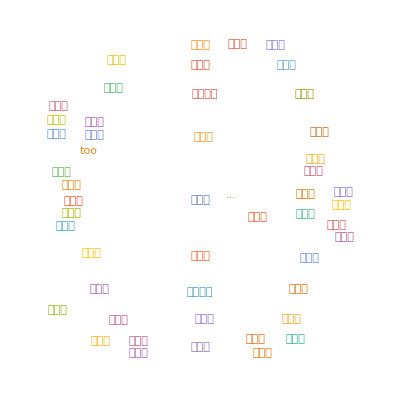

```mathematica
wordCloud=WordCloud[selected,MaxItems->50,FontFamily->"Microsoft JhengHei Light"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"cloud.png"}],Image[wordCloud,ImageSize->1024]]
```

D:\Machine Learning\Leraning\cloud.png

```mathematica
DeleteCases[data,{"（"}]
```

{这个,engineering,drawing,（,工程,作图,）,呢,，,我们,就,有,几年,用,鸭嘴,的,笔,，,旁边,一个,小盒子,。,最,痛苦,的,，,就是,鸭嘴笔,把,这个,水弄,到,里面,，,描图,的,时候,一下子,就,…,…,然后,就,用,刀片,刮,，,这个,就是,描图,最,痛苦,的,，,而且,这个,效率,efficiency,…,…,我,的,这个,经历,就是,到,了,上海,，,到,了,89,年,的,年初,的,时候,，,我,在,想,我,估计,是,快要,离休,了,，,我,想,我,应该,去,当,教授,。,于是,我,就,给,朱,物华,校长,、,张钟俊,这个,...,院长,，,给,他们,写,了,一个,报告,。,他们,说,欢迎,你,来,，,不过,，,这个,Apply,for,Professor,（,申请,当,教授,）,，,你,要,去,做,一个,报告,。,我,就,做,了,一个,能源,与,发展趋势,的,主要,的,节能,措施,，,这个,报告,经过,好几百个,教授,一致,通过,。,那么,上海交大,教授,当,了,以后,我,就,做,第二个,报告,，,就是,微电子,工业,的,发展,。,这,两个,报告,做,了,以后,不久,，,过后,，,1989,年,的,5,月,31,号,北京,就,把,我,调到,北京,去,了,。,现在,这个,报告,做,了,快,20,年,了,，,所以,呢,我,就,去年,呢,在,我们,交大,的,学报,，,我,发表,了,两篇,文章,，,就是,呼应,这个,89,年,的,报告,的,。,特别,是,昨天晚上,，,他,又,把,我,这个,第二篇,报告,，,还有,我,这,十几年,包括,在,电子,工业部,、,上海市,所,做,的,有,关于,信息,产业化,的,文章,，,总共,我,听,他们,讲,是,27,篇,…,…,我,也,没有,什么,别的,东西,送给,你们,，,我们,拿来,以后,我,叫,钱,秘书,啊,，,就,把,这,两个,学报,，,两个,学报,的,英文,本,─,─,因为,他们,这里,洋文,好,的,人,多得很,哪,─,─,英文,本,，,还有,前面,出过,两本书,，,再,加上,昨天晚上,出,的,这,本书,，,送给,郭伟华,同志,，,给,你,送过来,，,那么,给,你们,作为,一个,纪念,。,那么,人呐,就,都,不,知道,，,自己,就,不,可以,预料,。,一个,人,的,命运,啊,，,当然,要,靠,自我,奋斗,，,但是,也,要,考虑,到,历史,的,行程,。,我,绝对,不,知道,，,我,作为,一个,上海市委,书记,怎么,把,我,选到,北京,去,了,，,所以,邓小平,同志,跟,我,讲话,，,说,“,中央,都,决定,啦,，,你,来,当,总书记,”,，,我,说,另请高明,吧,。,我,实在,我,也,不是,谦虚,，,我,一个,上海市委,书记,怎么,到,北京,来,了,呢,？,但是,呢,，,小平,同志,讲,“,大家,已经,研究,决定,了,”,，,所以,后来,我,就,念,了,两首,诗,（,原话,如此,）,，,叫,“,苟利国家生死以,，,岂因祸福避趋之,”,，,那么,所以,我,就,到,了,北京,。,到,了,北京,我,干,了,这,十几年,也,没有,什么,别的,，,大概,三件,事,：,一个,，,确立,了,社会主义,市场经济,；,第二个,，,把,邓小平,的,理论,列入,了,党章,；,第三个,，,就是,我们,知道,的,“,三个代表,”,。,如果说,还有,一点,什么,成绩,，,就是,军队,一律,不得,经商,！,这个,对,军队,的,命运,有,很大,的,关系,。,因为,我,后来,又,干,了,一年,零八个,月,，,等于,我,在,部队,干,了,15,年,军委主席,。,还有,九八年,的,抗洪,也,是,很大,的,。,但,这些,都,是,次要,的,，,我,主要,的,我,就是,三件,事情,，,很,惭愧,，,就,做,了,一点,微小,的,工作,，,谢谢,大家,。,这,是,我,用,过,的,啊,？,老由,啊,，,现在,他们,文印,的,图章,里面,绝对,没有,这枚,图章,，,都,不,知道,有,这么,一个,东西,…,…,这就是说,明二院,的,档案,工作,做,得,太好了,！,你们,给,我,搞,的,这本,东西,啊,，,Excited,！,我们,需要,有所,选择,，,我们,希望,尽可能,地,限制,对,中国,发展,无用,的,信息,。,我,认为,所有,国家,和,政党,都,必须,有,他们,自己,的,出版物,来,宣传,他们,的,主张,，,我们,的确,有,新闻自由,，,但是,这种,自由,应该,从属,并,服从,于,国家,的,利益,。,我,个人,非常,痛恨,腐败,，,但,我,不,认为,这个,问题,能,在,一夜之间,解决,。,为了,逐步,根除,腐败,，,我们,需要,依靠,法治,的,办法,，,用,舆论,的,办法,、,教育,的,办法,逐步,地,把,它,解决,。,89,年,风波,期间,的确,有,学生,高呼,反对,腐败,的,口号,，,所以,在,这个,特定,的,问题,上,，,我们,党,和,青年,学生,是,站,在,同一,战线,上,的,。,但,事实上,还有,一小撮,别有用心,的,人,，,企图,利用,学生,的,热情,，,妄图,推翻,中国共产党,的,领导,并,颠覆,人民,民主专政,权,。,我们,不能允许,这种,事情,发生,。,我们,要,采取,坚决,的,措施,，,否则,我们,就,会,失去,努力,维系,至今,的,稳定,，,这,无论,对,中国,还是,对,世界,都,没,好处,。,我,只是,说明,这么,一个,问题,，,就是,这么,大,一个,国家,，,我们,有,12,亿多,人,，,新闻,的,对,国家,的,导向,确实,是,很,重要,的,。,你,不能,用,美国,的,价值观,来,对,中国,的,现状,做,评判,，,因为,你们,在,经济,、,国民教育,水平,上,高度发达,，,你,更,不能,把,美国,模式,强加于,中国,。,不管,中国,媒体,还是,外国,媒体,，,我,都,认为,有,一点,很,重要,，,那,就是,不能,歪曲事实,，,即便,他们,自己,由,发表,言论,的,自由,。,这,对,中国,媒体,很,重要,，,特别,是,我们,的,《,人民日报,》,，,我们,的,老百姓,非常重视,。,如果,它,把,某,一个,事实,报道,错误,了,，,人们,会,信以为真,。,我们,不像,你们,那儿,，,你们,想,报道,什么,就,报道,什么,，,就算,你们,的,报道,出,了,什么,错,也,无所谓,，,不会,有,很,严重,的,后果,。,比方说,，,我,现在,正在,北戴河,这儿,跟,你,交谈,，,但是,我,已经,看到,了,一些,外国,报纸,说,我,已经,到,了,大连,了,。,如果,是,真的,话,，,那,我,现在,怎么,可能,坐在,这里,跟,你,聊天,？,我,再,告诉,你,另,一件,事,。,几个,月,前,，,我,看到,一则,消息,说,“,江泽民,访问,厦门,，,突遭,炸弹,爆炸,重伤,送院,”,，,但,那,时候,我,还,在,北京,。,我,认为,部队,经商,是,一个,腐蚀剂,。,因为,历史,经验,已经,告诉,我们,，,任何,一个,国家,如果,军队,经商,以后,，,没有,一个,不,腐败,的,，,最后,必然,是,涣散,了,军心,。,一九四三年,的,时候,,,我,还,在,南京,上,大学,。,那时,日本,人,已经,占领,了,包括,南京,在内,的,许多,中国,领土,。,他们,希望,中国,老百姓,吸,鸦片烟,上瘾,,,所以,我们,自发,组织,了,反,鸦片,运动,，,捣毁,了,许多,烟馆,。,当,我们,遇到,日军,拿,着,刺刀,和,枪,指向,我们,的,时候,,,我们,就,唱,了,抗议,歌曲,《,毕业,歌,》,:,“,同学,们,！,大家,起来,！,担负起,天下,的,兴亡,！,听,吧,！,满耳是,大众,的,嗟,伤,;,看吧,！,一年,年,国土,的,沦丧,！,”,李洪志,这个,人,是,长春,人,，,不过,他,自己,说,他,是,释迦牟尼,的,再生,，,是,耶稣,的,再生,，,你,怎么,相信,？,他,说,世界,的,末日,就要,来临,，,说,地球,要,爆炸,了,。,而且,他,还,说,我,和,原来,的,李鹏,总理,给,他,打电话,，,叫,他,把,地球,的,毁灭,延后,几十年,，,但,我们,从来,就,没有,向,他,请求,过,。,他,企图,通过,这些,宣传,来,获得,信徒,的,信任,，,他,给,人,留下,一种,他,很,了解,中国,领导人,的,印象,其实,他,是,一派胡言,。,事实上,，,由于,他,的,传教,，,导致,许多,家庭,破裂,，,许多,人,也,因此,失去,生命,。,因此,经过,谨慎,的,考虑,，,我们,认为,“,法轮功,”,是,邪教,。,而且,，,“,法轮功,”,的,成员,也,从未,被判,过,死刑,。,不,需要,翻译,了,，,我,知道,你,想,说,什么,。,我,很,愿意,回答,这个,问题,，,因为,ABC,的,芭芭拉,沃尔特斯,十年,前,就,问过,我,同样,的,问题,，,而且,给,我,看,了,那个,照片,。,我,说,过,，,这个,年轻人,没有,被,逮捕,，,也,没有,受到,伤害,，,因为,坦克,在,他,面前,停下来,，,拒绝,碾过,他,。,芭芭拉,也,告诉,我,这个,年轻人,的,名字,，,我,可能,忘,了,，,但,我,问过,在,公共安全,情报,机关,工作,的,负责人,，,他们,利用,尽可能,多,的,关系,网络,来,寻找,这个,年轻人,，,经过,一个月,的,调查,，,我们,确信,这个,年轻人,并,没有,被捕,。,问,：,中国,的,北戴河,是不是,相当于,美国,的,戴维营,？,答,：,的确,是,它,是,一个,传统,，,每年,夏天,我们,的,中央,官员,都,会,来,这里,，,但,我们,来,这里,不是,度假,的,，,我们,还是,会,像,在,北京,一样,处理,日常事务,。,只不过,有时,会,去,游泳,。,我,的,医生,一直,在,建议,我,游泳,，,今早,我,就,去,游,了,一次,，,这,是,我,今年夏天,的,第,21,次,游泳,。,江主席,，,你,觉得,董先生,连任,好不好,啊,？,好,啊,。,中央,也,支持,他,吗,？,当然,啦,。,那,为什么,这么,早就,提出,了,，,有没有,别的,人选,呢,？,欧盟,呢,最近,发表,了,一个,报告,说,呢,…,…,呃,…,…,北京,会,透过,一些,渠道,去,影响,、,干预,香港,的,法治,，,你,对,这个,看法,有,什么,回应,呢,？,没,听到,这个,说法,。,是,彭定康,说,的,。,彭定康,…,…,你们,媒体,千万,要,注意,啊,，,不要,“,见,着,风,，,是,得,雨,”,啊,。,接到,这些,消息,，,你,媒体,本身,也,要,判断,，,明白,这,意思,吗,？,假使,这些,完全,…,…,无中生有,的,东西,，,你,再,帮,他,说,一遍,，,你,等于,…,这个,东西,…,你,...,你,也,有,责任,的,。,现在,还,那么,早,呢,你们,就是说,支持,董先生,呢,，,会,不会,给,人,感觉,就是,内定,了,、,是,钦点,了,董先生,呢,？,没有,…,…,没,任何,（,内定,、,钦点,）,的,意思,。,还是,按照,香港,的,…,…,按照,基本法,、,按照,选举,的,法,—,—,去,产生,…,…,但是,你们,能,不能,…,…,你,一,…,…,刚才,你,问,我,啊,，,我,可以,回答,你,一句,“,无可奉告,”,，,那,你们,又,不,高兴,，,那,怎么办,？,那,董先生,…,…,我,讲,的,意思,不是,我,是,钦点,他,当下,任,。,你,问,我,不支,支持,不,支持,，,我,说,支持,。,我,就,明确,给,你,告诉,这,一点,。,江主席,…,…,我,觉得,你们,啊,，,你们,我,感觉,你们,新闻界,还要,学习,一个,，,你们,非常,熟悉,西方,这,一套,的,Value,（,价值观,）,。,你们,毕竟,还,too,young,（,太,年轻,）,，,明白,我,的,意思,吧,。,我,告诉,你们,我,是,身经百战,了,，,见得,多,啦,！,啊,，,西方,的,哪,一个,国家,我,没,去过,？,媒体,他们,—,—,你,…,你们,要,知道,，,美国,的,华莱士,，,那比,你们,不,知道,高到,哪里,去,啦,！,啊,，,我,跟,他,谈笑风生,！,所以,说,媒体,啊,，,要,…,…,还是,要,提高,自己,的,知识,水平,！,懂,我,的,意思,—,—,识得,唔,识,得,啊,？,（,懂不懂,啊,？,）,唉,，,我,也,给,你们,着急,啊,，,真的,。,你们,今日,…,…,我,以为,…,…,遍地,…,…,你们,有,一个,好,，,全世界,跑,到,什么,地方,，,你们,比,其他,的,西方,记者,啊,，,跑,得,还,快,。,但是,呢,，,问来问去,的,问题,啊,，,都,too,simple,（,太,肤浅,）,，,啊,，,sometimes,na,?,ve,!,（,有时,很,幼稚,！,）,懂,了,没,啊,？,那,江主席,，,你,觉得,…,…,识得,唔,识,得,啊,？,（,一片,嘈杂声,）,但是,能,不能,说,一下,为什么,支持,董建华,呢,？,我,很,抱歉,，,我,今天,是,作为,一个,长者,，,跟,你们,讲,的,。,我,不是,新闻,工作者,，,但是,我,见得,太多,了,，,我,…,…,我,有,这个,必要,啊,告诉,你们,一点,，,人生,的,经验,。,我,刚才,呢,…,…,我,刚才,我,很,想,啊,，,就是,我,每,一次,碰到,你们,我,就,讲,，,中国,有,一句,话,叫,“,闷声,大,发财,”,。,我,就,什么,话,也,不用说,。,这是,最好,的,！,但是,我,想,我,见到,你们,这样,热情,啊,，,一句,话,不,说,也,不好,。,所以,你,刚才,你,一定,要,—,—,在,宣传,上,将来,如果,你们,报道,上,有,偏差,你们,要,负责,的,。,我,没有,说,要,钦定,（,董建华,）,，,没,任何,这个,意思,。,但是,你,问,…,…,你,一定,要不得,要,问,我,…,对,对,对,...,对,董先生,支持,不,支持,。,我们,不,支持,他,？,他,现在,是,当,特首,，,我们,怎么,能,不,支持,特首,？,但是,如果说,连任,呢,？,对,不,对,？,欸,，,连任,也,要,按照,香港,的,法律,啊,，,对,不,对,？,要,要,…,…,要,要,按照,香港,的,…,…,当然,，,我们,的,决定权,也,是,很,重要,的,。,香港,的,特区,…,…,特别,行政区,是,属于,中国,…,…,人民,共和,（,中华人民共和国,）,的,中央人民政府,啊,。,啊,？,到,那,时候,我们,会,表态,的,！,但是,呢,…,…,明白,这个,意思,吧,？,你们,啊,，,不要,想,…,…,喜欢,…,…,这,…,欸,弄,个,大,新闻,，,说,现在,已经,钦定,了,，,再,把,我,批判,一番,。,不是,，,但是,呢,就是,…,…,你们,啊,，,na,?,ve,!,（,幼稚,！,）,但是,呢,就是,…,…,好好,好,OKOK,…,…,I,',m,angry,!,（,我,生气,了,！,）,我,跟,你,讲,，,你们,这,样子,啊,，,那,不行,的,！,保安人员,：,好好,好,，,请,大家,离场,。,我,今天,算,得罪,了,你们,一下,！}